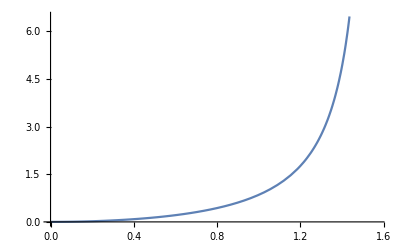

```mathematica
Plot[1/(Cos[x]-Cos[Pi/2])-1/(1-Cos[Pi/2]),{x,0,Pi/2}]
```

```mathematica
FullSimplify[D[Transpose[({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}})].({{Subscript[T, 11], Subscript[T, 12], Subscript[T, 13]}, {Subscript[T, 12], Subscript[T, 22], Subscript[T, 23]}, {Subscript[T, 13], Subscript[T, 23], Subscript[T, 33]}}).({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}),θ]]
```

{{1/2 (4 (Cos[θ] Cos[ϕ]^2 Sin[θ] T_11+Cos[2 θ] (Cos[ϕ] T_13+Sin[ϕ] T_23))+2 Sin[2 θ] (Sin[2 ϕ] T_12+Sin[ϕ]^2 T_22-T_33))}}

```mathematica
FullSimplify[D[Transpose[({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}})].({{Subscript[T, 11], Subscript[T, 12], Subscript[T, 13]}, {Subscript[T, 12], Subscript[T, 22], Subscript[T, 23]}, {Subscript[T, 13], Subscript[T, 23], Subscript[T, 33]}}).({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}),ϕ]]
```

{{2 Sin[θ] (-Cos[ϕ] Sin[θ] Sin[ϕ] T_11+Cos[2 ϕ] Sin[θ] T_12-Cos[θ] Sin[ϕ] T_13+Cos[ϕ] Sin[θ] Sin[ϕ] T_22+Cos[θ] Cos[ϕ] T_23)}}

```mathematica
FullSimplify[D[(Subscript[D, ij]-Sqrt[({Subscript[x, ij],Subscript[y, ij],Subscript[z, ij]}.({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}))^2])/((1-M)(Sqrt[({Subscript[x, ij],Subscript[y, ij],Subscript[z, ij]}.({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}))^2]-M*Subscript[D, ij])),ϕ]]
```

{(Sin[θ] D_ij (Sin[ϕ] x_ij-Cos[ϕ] y_ij) (Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij))/(√((Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij)^2) (-M D_ij+√((Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij)^2))^2)}

```mathematica
FullSimplify[D[(Subscript[D, ij]-Sqrt[({Subscript[x, ij],Subscript[y, ij],Subscript[z, ij]}.({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}))^2])/((1-M)(Sqrt[({Subscript[x, ij],Subscript[y, ij],Subscript[z, ij]}.({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}}))^2]-M*Subscript[D, ij])),θ]]
```

{-(D_ij (Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij) (Cos[θ] Cos[ϕ] x_ij+Cos[θ] Sin[ϕ] y_ij-Sin[θ] z_ij))/(√((Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij)^2) (-M D_ij+√((Cos[ϕ] Sin[θ] x_ij+Sin[θ] Sin[ϕ] y_ij+Cos[θ] z_ij)^2))^2)}

```mathematica
FullSimplify[D[(1-Sqrt[(Transpose[({{Sin[Subscript[θ, 1]]Cos[Subscript[ϕ, 1]]}, {Sin[Subscript[θ, 1]]Sin[Subscript[ϕ, 1]]}, {Cos[Subscript[θ, 1]]}})].({{Sin[Subscript[θ, 2]]Cos[Subscript[ϕ, 2]]}, {Sin[Subscript[θ, 2]]Sin[Subscript[ϕ, 2]]}, {Cos[Subscript[θ, 2]]}}))^2])/((1-M)(Sqrt[(Transpose[({{Sin[Subscript[θ, 1]]Cos[Subscript[ϕ, 1]]}, {Sin[Subscript[θ, 1]]Sin[Subscript[ϕ, 1]]}, {Cos[Subscript[θ, 1]]}})].({{Sin[Subscript[θ, 2]]Cos[Subscript[ϕ, 2]]}, {Sin[Subscript[θ, 2]]Sin[Subscript[ϕ, 2]]}, {Cos[Subscript[θ, 2]]}}))^2]-M)),Subscript[θ, 1]]]
```

{{((Cos[θ_2] Sin[θ_1]-Cos[θ_1] Cos[ϕ_1-ϕ_2] Sin[θ_2]) (Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2]))/(√((Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2])^2) (M-√((Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2])^2))^2)}}

```mathematica
FullSimplify[D[(1-Sqrt[(Transpose[({{Sin[Subscript[θ, 1]]Cos[Subscript[ϕ, 1]]}, {Sin[Subscript[θ, 1]]Sin[Subscript[ϕ, 1]]}, {Cos[Subscript[θ, 1]]}})].({{Sin[Subscript[θ, 2]]Cos[Subscript[ϕ, 2]]}, {Sin[Subscript[θ, 2]]Sin[Subscript[ϕ, 2]]}, {Cos[Subscript[θ, 2]]}}))^2])/((1-M)(Sqrt[(Transpose[({{Sin[Subscript[θ, 1]]Cos[Subscript[ϕ, 1]]}, {Sin[Subscript[θ, 1]]Sin[Subscript[ϕ, 1]]}, {Cos[Subscript[θ, 1]]}})].({{Sin[Subscript[θ, 2]]Cos[Subscript[ϕ, 2]]}, {Sin[Subscript[θ, 2]]Sin[Subscript[ϕ, 2]]}, {Cos[Subscript[θ, 2]]}}))^2]-M)),Subscript[ϕ, 1]]]
```

{{(Sin[θ_1] Sin[θ_2] (Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2]) Sin[ϕ_1-ϕ_2])/(√((Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2])^2) (M-√((Cos[θ_1] Cos[θ_2]+Cos[ϕ_1-ϕ_2] Sin[θ_1] Sin[θ_2])^2))^2)}}

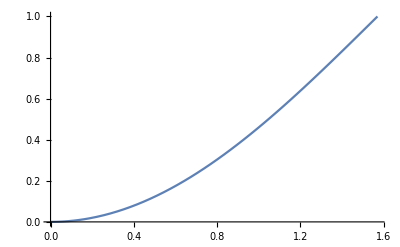

```mathematica
Plot[1-Cos[x],{x,0,Pi/2}]
```